## Sinobit from DXF exported from Eagle CAD

See stackexchange for details

```mathematica
SetDirectory["~/scad/Maerklin/mechanical"]
```

/home/cmaier/scad/Maerklin/mechanical

```mathematica
feilen=FileNames["sinobit_*.dxf"]
```

{sinobit_v1.0.dxf,sinobit_v1.1.dxf}

```mathematica
Import[#,{"DXF","Elements"}]&/@feilen
```

{{BoundaryMeshRegion,CoordinateTransform,Graphics3D,GraphicsComplex,LineData,LineObjects,MeshRegion,PlotRange,PointData,PointObjects,PolygonData,PolygonObjects,Region,Summary,VertexColors,VertexData,ViewPoint},{BoundaryMeshRegion,CoordinateTransform,Graphics3D,GraphicsComplex,LineData,LineObjects,MeshRegion,PlotRange,PointData,PointObjects,PolygonData,PolygonObjects,Region,Summary,VertexColors,VertexData,ViewPoint}}

```mathematica
rawdata=Import[#,{"DXF",{"LineObjects","PointObjects","PolygonObjects"}}]&/@feilen;
```

```mathematica
Dimensions[rawdata]
```

{2,3}

```mathematica
Dimensions/@rawdata
```

{{3},{3}}

```mathematica
Map[Dimensions,rawdata,{2}]
```

{{{1174},{0},{0}},{{1176},{0},{0}}}

```mathematica
Graphics3D[rawdata⟦1⟧]
```

-Graphics3D-

```mathematica
Graphics3D[rawdata⟦2⟧]
```

-Graphics3D-

### Center the data

```mathematica
Map[Dimensions,rawdata,{5}]
```

{{{Line[{{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3}}],1172,Line[{{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3}}]},{},{}},{{1},{},{}}}
 |  |  |  |

```mathematica
Map[Dimensions,rawdata⟦1⟧,{4}]
```

{{Line[{{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3}}],1172,Line[{{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3}}]},{},{}}
 |  |  |  |

```mathematica
Map[{Max[#],Min[#]}&,Transpose[Flatten[#/.Line->List,3]]&/@rawdata,{2}]
offsets=Map[(Plus@@##)/2&,%,{2}]
extents=Map[Subtract@@#&,%%,{2}]
```

{{{79.4004,-12.6492},{65.0748,-27.0256},{0.,0}},{{79.4004,-12.6492},{65.0748,-27.0256},{0.,0}}}

{{33.3756,19.0246,0.},{33.3756,19.0246,0.}}

{{92.0496,92.1004,0.},{92.0496,92.1004,0.}}

```mathematica
Dimensions[rawdata]
```

{2,3}

```mathematica
Dimensions[offsets]
```

{2,3}

```mathematica
?MapThread
```

MapThread[f,{{a_1,a_2,…},{b_1,b_2,…},…}] gives {f[a_1,b_1,…],f[a_2,b_2,…],…}. 
MapThread[f,{expr_1,expr_2,…},n] applies f to the parts of the expr_i at level n.

```mathematica
Dimensions[centereddata=MapThread[Function[{dxf,ofs},Map[#-ofs&,dxf,{4}]],{rawdata,offsets},1]]
```

{2,3}

```mathematica
Map[Dimensions,centereddata,{2}]
```

{{{1174},{0},{0}},{{1176},{0},{0}}}

```mathematica
Map[Print[Graphics3D[#]]&,centereddata,{1}];
```

-Graphics3D-

-Graphics3D-

### Outlines

Educated guess: the first line is the outline

```mathematica
Graphics3D[centereddata⟦1,1,1⟧]
```

-Graphics3D-

```mathematica
Graphics3D[centereddata⟦2,1,1⟧]
```

-Graphics3D-

#### Outline data

```mathematica
First[First[#]]&/@centereddata
```

{Line[{{-46.0248,-18.1569,0.},{-46.0168,-18.343,0.},{-45.9924,-18.5298,0.},{-45.9518,-18.7137,0.},{-45.8953,-18.8934,0.},{-45.8234,-19.0675,0.},{-45.7366,-19.2346,0.},{-45.6355,-19.3936,0.},{-45.521,-19.5431,0.},{-45.3939,-19.6821,0.},{-19.708,-45.4164,0.},{-19.7066,-45.4178,0.},{-19.5677,-45.5451,0.},{-19.4183,-45.6598,0.},{-19.2594,-45.7609,0.},{-19.0924,-45.8479,0.},{-18.9183,-45.92,0.},{-18.7387,-45.9766,0.},{-18.5548,-46.0174,0.},{-18.3681,-46.042,0.},{-18.1799,-46.0502,0.},{18.1307,-46.0502,0.},{18.3189,-46.0419,0.},{18.5056,-46.0172,0.},{18.6895,-45.9764,0.},{18.8691,-45.9197,0.},{19.0431,-45.8475,0.},{19.2101,-45.7604,0.},{19.3689,-45.6592,0.},{19.5183,-45.5444,0.},{19.6571,-45.4171,0.},{45.5046,-19.5453,0.},{45.6088,-19.4315,0.},{45.7033,-19.3084,0.},{45.7866,-19.1776,0.},{45.8582,-19.04,0.},{45.9176,-18.8967,0.},{45.9642,-18.7488,0.},{45.9978,-18.5974,0.},{46.018,-18.4436,0.},{46.0248,-18.2886,0.},{46.0248,18.1828,0.},{46.0168,18.369,0.},{45.9924,18.5558,0.},{45.9518,18.7397,0.},{45.8953,18.9194,0.},{45.8234,19.0934,0.},{45.7366,19.2606,0.},{45.6355,19.4195,0.},{45.521,19.5691,0.},{45.3939,19.7081,0.},{19.7334,45.4164,0.},{19.732,45.4178,0.},{19.5931,45.5451,0.},{19.4437,45.6597,0.},{19.2848,45.7609,0.},{19.1178,45.8479,0.},{18.9438,45.92,0.},{18.7641,45.9766,0.},{18.5802,46.0174,0.},{18.3935,46.042,0.},{18.2053,46.0502,0.},{-18.1055,46.0502,0.},{-18.2927,46.0421,0.},{-18.4794,46.0176,0.},{-18.6633,45.9769,0.},{-18.843,45.9203,0.},{-19.017,45.8483,0.},{-19.1841,45.7615,0.},{-19.343,45.6603,0.},{-19.4925,45.5457,0.},{-19.6314,45.4186,0.},{-45.3917,19.6825,0.},{-45.3924,19.6818,0.},{-45.5197,19.5429,0.},{-45.6344,19.3935,0.},{-45.7356,19.2346,0.},{-45.8225,19.0676,0.},{-45.8946,18.8935,0.},{-45.9512,18.7139,0.},{-45.992,18.53,0.},{-46.0166,18.3433,0.},{-46.0248,18.1551,0.},{-46.0248,-18.1569,0.},{-46.0248,-18.1569,0.}}],Line[{{-46.0248,-17.6578,0.},{-46.0122,-17.9456,0.},{-45.9746,-18.2312,0.},{-45.9123,-18.5124,0.},{-45.8257,-18.7871,0.},{-45.7154,-19.0533,0.},{-45.5824,-19.3088,0.},{-45.4276,-19.5517,0.},{-45.2523,-19.7803,0.},{-45.0588,-19.9915,0.},{-19.9919,-45.082,0.},{-19.7796,-45.2767,0.},{-19.5512,-45.4522,0.},{-19.3083,-45.607,0.},{-19.0529,-45.7402,0.},{-18.7868,-45.8505,0.},{-18.5121,-45.9373,0.},{-18.2309,-45.9998,0.},{-17.9453,-46.0375,0.},{-17.6575,-46.0502,0.},{-17.656,-46.0502,0.},{17.7058,-46.0502,0.},{17.9936,-46.0376,0.},{18.2792,-46.,0.},{18.5605,-45.9377,0.},{18.8352,-45.8511,0.},{19.1013,-45.7408,0.},{19.3568,-45.6078,0.},{19.5998,-45.453,0.},{19.8283,-45.2777,0.},{20.0407,-45.0831,0.},{20.0429,-45.0809,0.},{45.0599,-20.0168,0.},{45.2543,-19.8042,0.},{45.4294,-19.5755,0.},{45.584,-19.3324,0.},{45.7167,-19.0768,0.},{45.8267,-18.8105,0.},{45.9131,-18.5357,0.},{45.9752,-18.2544,0.},{46.0125,-17.9688,0.},{46.0248,-17.6841,0.},{46.0248,17.6814,0.},{46.0122,17.9691,0.},{45.9746,18.2547,0.},{45.9123,18.536,0.},{45.8257,18.8107,0.},{45.7154,19.0768,0.},{45.5824,19.3324,0.},{45.4276,19.5753,0.},{45.2523,19.8038,0.},{45.0577,20.0162,0.},{45.0566,20.0173,0.},{19.9661,45.0842,0.},{19.7537,45.2787,0.},{19.5251,45.4539,0.},{19.282,45.6086,0.},{19.0265,45.7415,0.},{18.7603,45.8516,0.},{18.4855,45.9381,0.},{18.2042,46.0003,0.},{17.9186,46.0378,0.},{17.6324,46.0502,0.},{-17.7313,46.0502,0.},{-18.0191,46.0376,0.},{-18.3047,46.,0.},{-18.5859,45.9377,0.},{-18.8606,45.8511,0.},{-19.1268,45.7408,0.},{-19.3823,45.6078,0.},{-19.6252,45.453,0.},{-19.8538,45.2777,0.},{-20.0661,45.0831,0.},{-20.0683,45.0809,0.},{-45.0598,20.0427,0.},{-45.2543,19.8301,0.},{-45.4294,19.6014,0.},{-45.584,19.3583,0.},{-45.7167,19.1027,0.},{-45.8267,18.8365,0.},{-45.9131,18.5617,0.},{-45.9752,18.2804,0.},{-46.0125,17.9947,0.},{-46.0248,17.71,0.},{-46.0248,-17.6578,0.},{-46.0248,-17.6578,0.}}]}

#### Get rid of 3rd coordinates

```mathematica
outlines2D=Map[Take[#,2]&,First[First[#]]&/@centereddata,{3}]
```

{Line[{{-46.0248,-18.1569},{-46.0168,-18.343},{-45.9924,-18.5298},{-45.9518,-18.7137},{-45.8953,-18.8934},{-45.8234,-19.0675},{-45.7366,-19.2346},{-45.6355,-19.3936},{-45.521,-19.5431},{-45.3939,-19.6821},{-19.708,-45.4164},{-19.7066,-45.4178},{-19.5677,-45.5451},{-19.4183,-45.6598},{-19.2594,-45.7609},{-19.0924,-45.8479},{-18.9183,-45.92},{-18.7387,-45.9766},{-18.5548,-46.0174},{-18.3681,-46.042},{-18.1799,-46.0502},{18.1307,-46.0502},{18.3189,-46.0419},{18.5056,-46.0172},{18.6895,-45.9764},{18.8691,-45.9197},{19.0431,-45.8475},{19.2101,-45.7604},{19.3689,-45.6592},{19.5183,-45.5444},{19.6571,-45.4171},{45.5046,-19.5453},{45.6088,-19.4315},{45.7033,-19.3084},{45.7866,-19.1776},{45.8582,-19.04},{45.9176,-18.8967},{45.9642,-18.7488},{45.9978,-18.5974},{46.018,-18.4436},{46.0248,-18.2886},{46.0248,18.1828},{46.0168,18.369},{45.9924,18.5558},{45.9518,18.7397},{45.8953,18.9194},{45.8234,19.0934},{45.7366,19.2606},{45.6355,19.4195},{45.521,19.5691},{45.3939,19.7081},{19.7334,45.4164},{19.732,45.4178},{19.5931,45.5451},{19.4437,45.6597},{19.2848,45.7609},{19.1178,45.8479},{18.9438,45.92},{18.7641,45.9766},{18.5802,46.0174},{18.3935,46.042},{18.2053,46.0502},{-18.1055,46.0502},{-18.2927,46.0421},{-18.4794,46.0176},{-18.6633,45.9769},{-18.843,45.9203},{-19.017,45.8483},{-19.1841,45.7615},{-19.343,45.6603},{-19.4925,45.5457},{-19.6314,45.4186},{-45.3917,19.6825},{-45.3924,19.6818},{-45.5197,19.5429},{-45.6344,19.3935},{-45.7356,19.2346},{-45.8225,19.0676},{-45.8946,18.8935},{-45.9512,18.7139},{-45.992,18.53},{-46.0166,18.3433},{-46.0248,18.1551},{-46.0248,-18.1569},{-46.0248,-18.1569}}],Line[{{-46.0248,-17.6578},{-46.0122,-17.9456},{-45.9746,-18.2312},{-45.9123,-18.5124},{-45.8257,-18.7871},{-45.7154,-19.0533},{-45.5824,-19.3088},{-45.4276,-19.5517},{-45.2523,-19.7803},{-45.0588,-19.9915},{-19.9919,-45.082},{-19.7796,-45.2767},{-19.5512,-45.4522},{-19.3083,-45.607},{-19.0529,-45.7402},{-18.7868,-45.8505},{-18.5121,-45.9373},{-18.2309,-45.9998},{-17.9453,-46.0375},{-17.6575,-46.0502},{-17.656,-46.0502},{17.7058,-46.0502},{17.9936,-46.0376},{18.2792,-46.},{18.5605,-45.9377},{18.8352,-45.8511},{19.1013,-45.7408},{19.3568,-45.6078},{19.5998,-45.453},{19.8283,-45.2777},{20.0407,-45.0831},{20.0429,-45.0809},{45.0599,-20.0168},{45.2543,-19.8042},{45.4294,-19.5755},{45.584,-19.3324},{45.7167,-19.0768},{45.8267,-18.8105},{45.9131,-18.5357},{45.9752,-18.2544},{46.0125,-17.9688},{46.0248,-17.6841},{46.0248,17.6814},{46.0122,17.9691},{45.9746,18.2547},{45.9123,18.536},{45.8257,18.8107},{45.7154,19.0768},{45.5824,19.3324},{45.4276,19.5753},{45.2523,19.8038},{45.0577,20.0162},{45.0566,20.0173},{19.9661,45.0842},{19.7537,45.2787},{19.5251,45.4539},{19.282,45.6086},{19.0265,45.7415},{18.7603,45.8516},{18.4855,45.9381},{18.2042,46.0003},{17.9186,46.0378},{17.6324,46.0502},{-17.7313,46.0502},{-18.0191,46.0376},{-18.3047,46.},{-18.5859,45.9377},{-18.8606,45.8511},{-19.1268,45.7408},{-19.3823,45.6078},{-19.6252,45.453},{-19.8538,45.2777},{-20.0661,45.0831},{-20.0683,45.0809},{-45.0598,20.0427},{-45.2543,19.8301},{-45.4294,19.6014},{-45.584,19.3583},{-45.7167,19.1027},{-45.8267,18.8365},{-45.9131,18.5617},{-45.9752,18.2804},{-46.0125,17.9947},{-46.0248,17.71},{-46.0248,-17.6578},{-46.0248,-17.6578}}]}

#### String convert to SCAD polygon syntax

```mathematica
outlinepolygons=StringReplace[StringReplace[ToString[#],{"Line["->"polygon(","]"->");"}],{"{"->"[","}"->"]"}]&/@outlines2D
```

{polygon([[-46.0248, -18.1569], [-46.0168, -18.343], [-45.9924, -18.5298], [-45.9518, -18.7137], [-45.8953, -18.8934], [-45.8234, -19.0675], [-45.7366, -19.2346], [-45.6355, -19.3936], [-45.521, -19.5431], [-45.3939, -19.6821], [-19.708, -45.4164], [-19.7066, -45.4178], [-19.5677, -45.5451], [-19.4183, -45.6598], [-19.2594, -45.7609], [-19.0924, -45.8479], [-18.9183, -45.92], [-18.7387, -45.9766], [-18.5548, -46.0174], [-18.3681, -46.042], [-18.1799, -46.0502], [18.1307, -46.0502], [18.3189, -46.0419], [18.5056, -46.0172], [18.6895, -45.9764], [18.8691, -45.9197], [19.0431, -45.8475], [19.2101, -45.7604], [19.3689, -45.6592], [19.5183, -45.5444], [19.6571, -45.4171], [45.5046, -19.5453], [45.6088, -19.4315], [45.7033, -19.3084], [45.7866, -19.1776], [45.8582, -19.04], [45.9176, -18.8967], [45.9642, -18.7488], [45.9978, -18.5974], [46.018, -18.4436], [46.0248, -18.2886], [46.0248, 18.1828], [46.0168, 18.369], [45.9924, 18.5558], [45.9518, 18.7397], [45.8953, 18.9194], [45.8234, 19.0934], [45.7366, 19.2606], [45.6355, 19.4195], [45.521, 19.5691], [45.3939, 19.7081], [19.7334, 45.4164], [19.732, 45.4178], [19.5931, 45.5451], [19.4437, 45.6597], [19.2848, 45.7609], [19.1178, 45.8479], [18.9438, 45.92], [18.7641, 45.9766], [18.5802, 46.0174], [18.3935, 46.042], [18.2053, 46.0502], [-18.1055, 46.0502], [-18.2927, 46.0421], [-18.4794, 46.0176], [-18.6633, 45.9769], [-18.843, 45.9203], [-19.017, 45.8483], [-19.1841, 45.7615], [-19.343, 45.6603], [-19.4925, 45.5457], [-19.6314, 45.4186], [-45.3917, 19.6825], [-45.3924, 19.6818], [-45.5197, 19.5429], [-45.6344, 19.3935], [-45.7356, 19.2346], [-45.8225, 19.0676], [-45.8946, 18.8935], [-45.9512, 18.7139], [-45.992, 18.53], [-46.0166, 18.3433], [-46.0248, 18.1551], [-46.0248, -18.1569], [-46.0248, -18.1569]]);,polygon([[-46.0248, -17.6578], [-46.0122, -17.9456], [-45.9746, -18.2312], [-45.9123, -18.5124], [-45.8257, -18.7871], [-45.7154, -19.0533], [-45.5824, -19.3088], [-45.4276, -19.5517], [-45.2523, -19.7803], [-45.0588, -19.9915], [-19.9919, -45.082], [-19.7796, -45.2767], [-19.5512, -45.4522], [-19.3083, -45.607], [-19.0529, -45.7402], [-18.7868, -45.8505], [-18.5121, -45.9373], [-18.2309, -45.9998], [-17.9453, -46.0375], [-17.6575, -46.0502], [-17.656, -46.0502], [17.7058, -46.0502], [17.9936, -46.0376], [18.2792, -46.], [18.5605, -45.9377], [18.8352, -45.8511], [19.1013, -45.7408], [19.3568, -45.6078], [19.5998, -45.453], [19.8283, -45.2777], [20.0407, -45.0831], [20.0429, -45.0809], [45.0599, -20.0168], [45.2543, -19.8042], [45.4294, -19.5755], [45.584, -19.3324], [45.7167, -19.0768], [45.8267, -18.8105], [45.9131, -18.5357], [45.9752, -18.2544], [46.0125, -17.9688], [46.0248, -17.6841], [46.0248, 17.6814], [46.0122, 17.9691], [45.9746, 18.2547], [45.9123, 18.536], [45.8257, 18.8107], [45.7154, 19.0768], [45.5824, 19.3324], [45.4276, 19.5753], [45.2523, 19.8038], [45.0577, 20.0162], [45.0566, 20.0173], [19.9661, 45.0842], [19.7537, 45.2787], [19.5251, 45.4539], [19.282, 45.6086], [19.0265, 45.7415], [18.7603, 45.8516], [18.4855, 45.9381], [18.2042, 46.0003], [17.9186, 46.0378], [17.6324, 46.0502], [-17.7313, 46.0502], [-18.0191, 46.0376], [-18.3047, 46.], [-18.5859, 45.9377], [-18.8606, 45.8511], [-19.1268, 45.7408], [-19.3823, 45.6078], [-19.6252, 45.453], [-19.8538, 45.2777], [-20.0661, 45.0831], [-20.0683, 45.0809], [-45.0598, 20.0427], [-45.2543, 19.8301], [-45.4294, 19.6014], [-45.584, 19.3583], [-45.7167, 19.1027], [-45.8267, 18.8365], [-45.9131, 18.5617], [-45.9752, 18.2804], [-46.0125, 17.9947], [-46.0248, 17.71], [-46.0248, -17.6578], [-46.0248, -17.6578]]);}

#### Export polygon strings

```mathematica
MapThread[Export[#1,#2,"Text"]&,{StringReplace[feilen,"dxf"->"2doutline.scad"],outlinepolygons}]
```

{sinobit_v1.0.2doutline.scad,sinobit_v1.1.2doutline.scad}

### Try to make sense of more internal lines

#### Find holes by binary search

```mathematica
Print[Graphics3D[Take[First[centereddata⟦1⟧],{717,724}]]]
```

-Graphics3D-

```mathematica
Print[Graphics3D[Take[First[centereddata⟦-1⟧],{721,728}]]]
```

-Graphics3D-

```mathematica
holes=Map[Take[#,2]&,MapThread[Take[First[#1],#2]&,{centereddata,{{717,724},{721,728}}}],{4}];
```

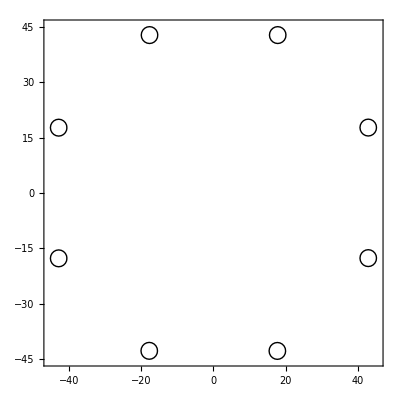

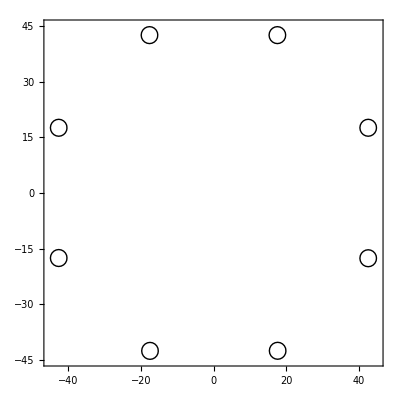

```mathematica
Print[Graphics[#,Frame->True]]&/@holes;
```

```mathematica
Dimensions[holes]
```

{2,8}

```mathematica
Map[Dimensions,holes,{3}]
```

{{Line[{21,2}],Line[{21,2}],Line[{21,2}],Line[{21,2}],Line[{21,2}],Line[{21,2}],Line[{21,2}],Line[{21,2}]},{Line[{21,2}],Line[{21,2}],Line[{21,2}],Line[{21,2}],Line[{21,2}],Line[{21,2}],Line[{21,2}],Line[{21,2}]}}

```mathematica
Dimensions[holes/.Line->List]
```

{2,8,1,21,2}

```mathematica
Map[{Max[#],Min[#]}&/@Transpose[First[#]]&,holes,{2}]
Map[(Plus@@##)/2&,%,{3}]
Map[Subtract@@##&,%%,{3}]
```

{{{{45.085,40.513},{20.0406,15.4686}},{{45.085,40.513},{-15.3828,-19.9548}},{{-15.3924,-19.9644},{45.1372,40.5652}},{{19.9548,15.3828},{-40.5636,-45.1356}},{{-15.4686,-20.0406},{-40.5384,-45.1104}},{{-40.513,-45.085},{-15.4432,-20.0152}},{{-40.513,-45.085},{20.0152,15.4432}},{{20.0532,15.4812},{45.1372,40.5652}}},{{{-40.3352,-44.9072},{19.8882,15.3162}},{{-40.3352,-44.9072},{-15.2558,-19.8278}},{{19.8374,15.2654},{44.8832,40.3112}},{{-15.2146,-19.7866},{-40.3096,-44.8816}},{{19.9136,15.3416},{-40.2844,-44.8564}},{{44.831,40.259},{-15.3162,-19.8882}},{{44.831,40.259},{19.8882,15.3162}},{{-15.3542,-19.9262},{44.8832,40.3112}}}}

{{{42.799,17.7546},{42.799,-17.6688},{-17.6784,42.8512},{17.6688,-42.8496},{-17.7546,-42.8244},{-42.799,-17.7292},{-42.799,17.7292},{17.7672,42.8512}},{{-42.6212,17.6022},{-42.6212,-17.5418},{17.5514,42.5972},{-17.5006,-42.5956},{17.6276,-42.5704},{42.545,-17.6022},{42.545,17.6022},{-17.6402,42.5972}}}

{{{4.572,4.572},{4.572,4.572},{4.572,4.572},{4.572,4.572},{4.572,4.572},{4.572,4.572},{4.572,4.572},{4.572,4.572}},{{4.572,4.572},{4.572,4.572},{4.572,4.572},{4.572,4.572},{4.572,4.572},{4.572,4.572},{4.572,4.572},{4.572,4.572}}}

```mathematica
holepolygons=Map[StringReplace[StringReplace[ToString[#],{"Line["->"polygon(","]"->");"}],{"{"->"[","}"->"]"}]&,holes,{2}]
```

{{polygon([[45.085, 17.7546], [44.9731, 18.461], [44.6484, 19.0983], [44.1427, 19.604], [43.5054, 19.9287], [42.799, 20.0406], [42.0926, 19.9287], [41.4553, 19.604], [40.9496, 19.0983], [40.6249, 18.461], [40.513, 17.7546], [40.6249, 17.0482], [40.9496, 16.4109], [41.4553, 15.9052], [42.0926, 15.5805], [42.799, 15.4686], [43.5054, 15.5805], [44.1427, 15.9052], [44.6484, 16.4109], [44.9731, 17.0482], [45.085, 17.7546]]);,polygon([[45.085, -17.6688], [44.9731, -16.9624], [44.6484, -16.3251], [44.1427, -15.8194], [43.5054, -15.4947], [42.799, -15.3828], [42.0926, -15.4947], [41.4553, -15.8194], [40.9496, -16.3251], [40.6249, -16.9624], [40.513, -17.6688], [40.6249, -18.3752], [40.9496, -19.0125], [41.4553, -19.5182], [42.0926, -19.8429], [42.799, -19.9548], [43.5054, -19.8429], [44.1427, -19.5182], [44.6484, -19.0125], [44.9731, -18.3752], [45.085, -17.6688]]);,polygon([[-15.3924, 42.8512], [-15.5043, 43.5576], [-15.829, 44.1949], [-16.3347, 44.7006], [-16.972, 45.0253], [-17.6784, 45.1372], [-18.3848, 45.0253], [-19.0221, 44.7006], [-19.5278, 44.1949], [-19.8525, 43.5576], [-19.9644, 42.8512], [-19.8525, 42.1448], [-19.5278, 41.5075], [-19.0221, 41.0018], [-18.3848, 40.6771], [-17.6784, 40.5652], [-16.972, 40.6771], [-16.3347, 41.0018], [-15.829, 41.5075], [-15.5043, 42.1448], [-15.3924, 42.8512]]);,polygon([[19.9548, -42.8496], [19.8429, -42.1432], [19.5182, -41.5059], [19.0125, -41.0002], [18.3752, -40.6755], [17.6688, -40.5636], [16.9624, -40.6755], [16.3251, -41.0002], [15.8194, -41.5059], [15.4947, -42.1432], [15.3828, -42.8496], [15.4947, -43.556], [15.8194, -44.1933], [16.3251, -44.699], [16.9624, -45.0237], [17.6688, -45.1356], [18.3752, -45.0237], [19.0125, -44.699], [19.5182, -44.1933], [19.8429, -43.556], [19.9548, -42.8496]]);,polygon([[-15.4686, -42.8244], [-15.5805, -42.118], [-15.9052, -41.4807], [-16.4109, -40.975], [-17.0482, -40.6503], [-17.7546, -40.5384], [-18.461, -40.6503], [-19.0983, -40.975], [-19.604, -41.4807], [-19.9287, -42.118], [-20.0406, -42.8244], [-19.9287, -43.5308], [-19.604, -44.1681], [-19.0983, -44.6738], [-18.461, -44.9985], [-17.7546, -45.1104], [-17.0482, -44.9985], [-16.4109, -44.6738], [-15.9052, -44.1681], [-15.5805, -43.5308], [-15.4686, -42.8244]]);,polygon([[-40.513, -17.7292], [-40.6249, -17.0228], [-40.9496, -16.3855], [-41.4553, -15.8798], [-42.0926, -15.5551], [-42.799, -15.4432], [-43.5054, -15.5551], [-44.1427, -15.8798], [-44.6484, -16.3855], [-44.9731, -17.0228], [-45.085, -17.7292], [-44.9731, -18.4356], [-44.6484, -19.0729], [-44.1427, -19.5786], [-43.5054, -19.9033], [-42.799, -20.0152], [-42.0926, -19.9033], [-41.4553, -19.5786], [-40.9496, -19.0729], [-40.6249, -18.4356], [-40.513, -17.7292]]);,polygon([[-40.513, 17.7292], [-40.6249, 18.4356], [-40.9496, 19.0729], [-41.4553, 19.5786], [-42.0926, 19.9033], [-42.799, 20.0152], [-43.5054, 19.9033], [-44.1427, 19.5786], [-44.6484, 19.0729], [-44.9731, 18.4356], [-45.085, 17.7292], [-44.9731, 17.0228], [-44.6484, 16.3855], [-44.1427, 15.8798], [-43.5054, 15.5551], [-42.799, 15.4432], [-42.0926, 15.5551], [-41.4553, 15.8798], [-40.9496, 16.3855], [-40.6249, 17.0228], [-40.513, 17.7292]]);,polygon([[20.0532, 42.8512], [19.9413, 43.5576], [19.6166, 44.1949], [19.1109, 44.7006], [18.4736, 45.0253], [17.7672, 45.1372], [17.0608, 45.0253], [16.4235, 44.7006], [15.9178, 44.1949], [15.5931, 43.5576], [15.4812, 42.8512], [15.5931, 42.1448], [15.9178, 41.5075], [16.4235, 41.0018], [17.0608, 40.6771], [17.7672, 40.5652], [18.4736, 40.6771], [19.1109, 41.0018], [19.6166, 41.5075], [19.9413, 42.1448], [20.0532, 42.8512]]);},{polygon([[-40.3352, 17.6022], [-40.4471, 18.3086], [-40.7718, 18.9459], [-41.2775, 19.4516], [-41.9148, 19.7763], [-42.6212, 19.8882], [-43.3276, 19.7763], [-43.9649, 19.4516], [-44.4706, 18.9459], [-44.7953, 18.3086], [-44.9072, 17.6022], [-44.7953, 16.8958], [-44.4706, 16.2585], [-43.9649, 15.7528], [-43.3276, 15.4281], [-42.6212, 15.3162], [-41.9148, 15.4281], [-41.2775, 15.7528], [-40.7718, 16.2585], [-40.4471, 16.8958], [-40.3352, 17.6022]]);,polygon([[-40.3352, -17.5418], [-40.4471, -16.8354], [-40.7718, -16.1981], [-41.2775, -15.6924], [-41.9148, -15.3677], [-42.6212, -15.2558], [-43.3276, -15.3677], [-43.9649, -15.6924], [-44.4706, -16.1981], [-44.7953, -16.8354], [-44.9072, -17.5418], [-44.7953, -18.2482], [-44.4706, -18.8855], [-43.9649, -19.3912], [-43.3276, -19.7159], [-42.6212, -19.8278], [-41.9148, -19.7159], [-41.2775, -19.3912], [-40.7718, -18.8855], [-40.4471, -18.2482], [-40.3352, -17.5418]]);,polygon([[19.8374, 42.5972], [19.7255, 43.3036], [19.4008, 43.9409], [18.8951, 44.4466], [18.2578, 44.7713], [17.5514, 44.8832], [16.845, 44.7713], [16.2077, 44.4466], [15.702, 43.9409], [15.3773, 43.3036], [15.2654, 42.5972], [15.3773, 41.8908], [15.702, 41.2535], [16.2077, 40.7478], [16.845, 40.4231], [17.5514, 40.3112], [18.2578, 40.4231], [18.8951, 40.7478], [19.4008, 41.2535], [19.7255, 41.8908], [19.8374, 42.5972]]);,polygon([[-15.2146, -42.5956], [-15.3265, -41.8892], [-15.6512, -41.2519], [-16.1569, -40.7462], [-16.7942, -40.4215], [-17.5006, -40.3096], [-18.207, -40.4215], [-18.8443, -40.7462], [-19.35, -41.2519], [-19.6747, -41.8892], [-19.7866, -42.5956], [-19.6747, -43.302], [-19.35, -43.9393], [-18.8443, -44.445], [-18.207, -44.7697], [-17.5006, -44.8816], [-16.7942, -44.7697], [-16.1569, -44.445], [-15.6512, -43.9393], [-15.3265, -43.302], [-15.2146, -42.5956]]);,polygon([[19.9136, -42.5704], [19.8017, -41.864], [19.477, -41.2267], [18.9713, -40.721], [18.334, -40.3963], [17.6276, -40.2844], [16.9212, -40.3963], [16.2839, -40.721], [15.7782, -41.2267], [15.4535, -41.864], [15.3416, -42.5704], [15.4535, -43.2768], [15.7782, -43.9141], [16.2839, -44.4198], [16.9212, -44.7445], [17.6276, -44.8564], [18.334, -44.7445], [18.9713, -44.4198], [19.477, -43.9141], [19.8017, -43.2768], [19.9136, -42.5704]]);,polygon([[44.831, -17.6022], [44.7191, -16.8958], [44.3944, -16.2585], [43.8887, -15.7528], [43.2514, -15.4281], [42.545, -15.3162], [41.8386, -15.4281], [41.2013, -15.7528], [40.6956, -16.2585], [40.3709, -16.8958], [40.259, -17.6022], [40.3709, -18.3086], [40.6956, -18.9459], [41.2013, -19.4516], [41.8386, -19.7763], [42.545, -19.8882], [43.2514, -19.7763], [43.8887, -19.4516], [44.3944, -18.9459], [44.7191, -18.3086], [44.831, -17.6022]]);,polygon([[44.831, 17.6022], [44.7191, 18.3086], [44.3944, 18.9459], [43.8887, 19.4516], [43.2514, 19.7763], [42.545, 19.8882], [41.8386, 19.7763], [41.2013, 19.4516], [40.6956, 18.9459], [40.3709, 18.3086], [40.259, 17.6022], [40.3709, 16.8958], [40.6956, 16.2585], [41.2013, 15.7528], [41.8386, 15.4281], [42.545, 15.3162], [43.2514, 15.4281], [43.8887, 15.7528], [44.3944, 16.2585], [44.7191, 16.8958], [44.831, 17.6022]]);,polygon([[-15.3542, 42.5972], [-15.4661, 43.3036], [-15.7908, 43.9409], [-16.2965, 44.4466], [-16.9338, 44.7713], [-17.6402, 44.8832], [-18.3466, 44.7713], [-18.9839, 44.4466], [-19.4896, 43.9409], [-19.8143, 43.3036], [-19.9262, 42.5972], [-19.8143, 41.8908], [-19.4896, 41.2535], [-18.9839, 40.7478], [-18.3466, 40.4231], [-17.6402, 40.3112], [-16.9338, 40.4231], [-16.2965, 40.7478], [-15.7908, 41.2535], [-15.4661, 41.8908], [-15.3542, 42.5972]]);}}

```mathematica
MapThread[Export[#1,#2,"Text"]&,{StringReplace[feilen,"dxf"->"2holes.scad"],holepolygons}]
```

{sinobit_v1.0.2holes.scad,sinobit_v1.1.2holes.scad}

## Sinobit from numbers

### Octagon

```mathematica
width=3.625 25.4
```

92.075

```mathematica
CirclePoints[8]
```

{{Sin[π/8],-Cos[π/8]},{Cos[π/8],-Sin[π/8]},{Cos[π/8],Sin[π/8]},{Sin[π/8],Cos[π/8]},{-Sin[π/8],Cos[π/8]},{-Cos[π/8],Sin[π/8]},{-Cos[π/8],-Sin[π/8]},{-Sin[π/8],-Cos[π/8]}}

```mathematica
CirclePoints[8]/(2 Cos[π/8])
```

{{1/2 Tan[π/8],-1/2},{1/2,-1/2 Tan[π/8]},{1/2,1/2 Tan[π/8]},{1/2 Tan[π/8],1/2},{-1/2 Tan[π/8],1/2},{-1/2,1/2 Tan[π/8]},{-1/2,-1/2 Tan[π/8]},{-1/2 Tan[π/8],-1/2}}

```mathematica
N[π/8/°]
```

22.5

### Holes

```mathematica
holecos=42.8
```

42.8

```mathematica
holesin=holecos Tan[π/8]
```

17.7283

```mathematica
holer=4.572/2
```

2.286

### Miter radius

```mathematica
CirclePoints[8]/(2 Cos[π/8])width
```

{{19.0694,-46.0375},{46.0375,-19.0694},{46.0375,19.0694},{19.0694,46.0375},{-19.0694,46.0375},{-46.0375,19.0694},{-46.0375,-19.0694},{-19.0694,-46.0375}}

```mathematica
width/2-holecos
```

3.2375